```mathematica
Needs["VectorFieldPlots`"]
```

Also plot the initial condition for r1, r2 to show that it can't go out of the viable region.

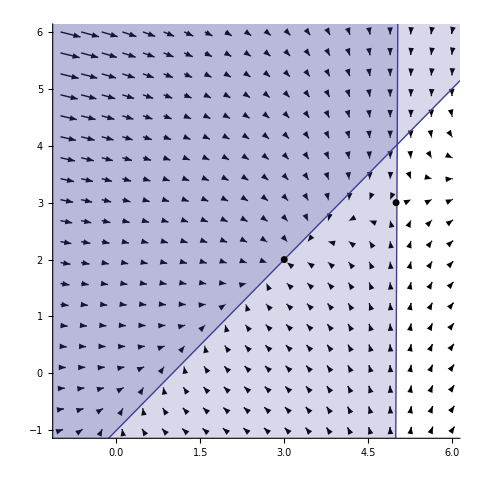

```mathematica
par={x0->1,y0->5,z0->1};
min=-1;max=6;
g1=VectorFieldPlot[{(-r1+r2+x0)(-r1+y0),(r1-2r2+z0)}/.par,{r1,min,max},{r2,min,max},PlotPoints->20];
g2=Plot[1000/y0 r1-1000/.par,{r1,5min,5max},Filling->Top];
g3=Plot[r1-x0/.par,{r1,5min,5max},Filling->Top];
Show[g1,g2,g3,Graphics[{AbsolutePointSize[5],Point[{y0,(y0+z0)/2}/.par],Point[{2 x0+z0,x0+z0}/.par]}],Axes->True,PlotRange->{{min,max},{min,max}}]
```

```mathematica
sol=Solve[{(-r1+r2+x0)(-r1+y0)==0,(r1-2r2+z0)^2==0},{r1,r2}]
```

{{r1→y0,r2→(y0+z0)/2},{r1→y0,r2→(y0+z0)/2},{r1→2 x0+z0,r2→x0+z0},{r1→2 x0+z0,r2→x0+z0}}

Note: Sometimes one of these points may not be physically realietic.

```mathematica
f1=(-r1+r2+x0)(-r1+y0)
f2=(r1-2r2+z0)^2
```

(-r1+r2+x0) (-r1+y0)

(r1-2 r2+z0)^2

```mathematica
A={
{D[f1,r1],D[f1,r2]},
{D[f2,r1],D[f2,r2]}
};
A//MatrixForm
```

(2 r1-r2-x0-y0 | -r1+y0
2 (r1-2 r2+z0) | -4 (r1-2 r2+z0))

```mathematica
A/.sol⟦1⟧//MatrixForm
a=Eigenvalues[A/.sol⟦1⟧]
```

(-x0+y0+1/2 (-y0-z0) | 0
0 | 0)

{0,-x0+y0+1/2 (-y0-z0)}

```mathematica
A/.sol⟦3⟧//MatrixForm
b=Simplify[Eigenvalues[A/.sol⟦3⟧]]
```

(-2 x0-y0-z0+2 (2 x0+z0) | -2 x0+y0-z0
2 (2 x0+2 z0-2 (x0+z0)) | -4 (2 x0+2 z0-2 (x0+z0)))

{0,2 x0-y0+z0}